# Tutorial of Eos

## Initialization

Change to the path to the folder Eos (grey text). Attention: (i) Always use variable $eosUserDirectory to set the path, and  (ii) Do not run the 5 lines below since they are set to be initialization cells.

```mathematica
$eosUserDirectory="/Users/Origami/Dropbox/Tutorial/Eos";
```

```mathematica
AppendTo[$Path,$eosUserDirectory];
```

```mathematica
<<Eos`
```

Eos3: 1.01(November 6, 2018)

```mathematica
Exact[]
```

Ok (Exact)

```mathematica
InteractiveFold[False]
```

Ok(non-interactive)

## Segment trisection - Haga method

### Construction

```mathematica
BeginOrigami[10]
```

-Graphics3D-

```mathematica
HO["A","D"]
```

-Graphics3D-

```mathematica
Unfold[]
```

-Graphics3D-

```mathematica
HO["C","E",MarkPointOn-> {{"AB","G"}}]
```

-Graphics3D-

```mathematica
HO["BC",Handle-> {"A"},MarkPointOn-> {{"AG","P"}}]
```

-Graphics3D-

```mathematica
UnfoldAll[]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["P","B"]
```

10/3

### Proof

```mathematica
map={"A"-> {0, 0} ,"B"-> {r, 0}, "C"-> {r, r}, "D"-> {0,r}}
```

{A→{0,0},B→{r,0},C→{r,r},D→{0,r}}

```mathematica
Prove["Segment trisection- Haga's method",Goal->9* SquaredDistance["P","B"]== SquaredDistance["A","B"],Mapping-> map]
```

ProofbyGB::gbstart: Proof by Groebner basis method started at November 14, 2018 4:36:37 PM JST.

ProofbyGB::gbsuccess: Proof by Groebner basis method is successful.

CPU time used for Groebner basis computation is 0.04991  seconds.

{True,0.04991,Segment trisection- Haga's method.nb/Users/Origami/Dropbox/Tutorial/EosProofDoc/Segment trisection- Haga's method.nbNone/Users/Origami/Dropbox/Tutorial/EosProofDoc/Segment trisection- Haga's method.nb}

## Segment division

### Construction

```mathematica
EosSession["Recursive Haga theorem"]
```

Recursive Haga theorem.0

Recursive Haga theorem

```mathematica
BeginOrigami[]
```

Recursive Haga theorem.1

-Graphics3D-

```mathematica
HO["A","D"]
```

Recursive Haga theorem.2

-Graphics3D-

```mathematica
Unfold[]
```

Recursive Haga theorem.3

-Graphics3D-

```mathematica
HO["C","E",MarkPointOn-> {{"AB","G"}}]
```

Recursive Haga theorem.4

-Graphics3D-

```mathematica
HO["BC",Handle-> {"A"},MarkPointOn-> {{"AG","P"}}]
```

Recursive Haga theorem.5

-Graphics3D-

```mathematica
UnfoldAll[]
```

Recursive Haga theorem.7

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["P","B"]
```

Recursive Haga theorem.7

1/3

```mathematica
HO["D","P"]
```

Recursive Haga theorem.8

-Graphics3D-

```mathematica
HO["DC",Handle-> "B"]
```

Recursive Haga theorem.9

-Graphics3D-

```mathematica
UnfoldAll[]
```

Recursive Haga theorem.11

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["K","C"]
```

Recursive Haga theorem.11

1/5

```mathematica
HO["A","K",MarkPointOn-> {{"DC","Z"}}]
```

Recursive Haga theorem.12

-Graphics3D-

```mathematica
HO["DA",Handle-> "B",MarkPointOn-> {{"ZC","W"}}]
```

Recursive Haga theorem.13

-Graphics3D-

```mathematica
UnfoldAll[]
```

Recursive Haga theorem.15

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["D","W"]
```

Recursive Haga theorem.15

1/9

```mathematica
HO["B","W",MarkPointOn-> {{"AD","T"}}]
```

Recursive Haga theorem.16

-Graphics3D-

```mathematica
HO["AB",Handle-> "C",MarkPointOn-> {{"DT", "U"}}]
```

Recursive Haga theorem.17

-Graphics3D-

```mathematica
UnfoldAll[]
```

Recursive Haga theorem.19

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["A","U"]
```

Recursive Haga theorem.19

1/17

```mathematica
HO["C","U"]
```

Recursive Haga theorem.20

-Graphics3D-

```mathematica
HO["BC",Handle-> "A",MarkPointOn-> {{"AL", "V"}}]
```

Recursive Haga theorem.21

-Graphics3D-

```mathematica
UnfoldAll[]
```

Recursive Haga theorem.23

{-Graphics3D-,-Graphics3D-}

```mathematica
Distance["B","V"]
```

Recursive Haga theorem.23

1/33

```mathematica
$origami== 23
```

Recursive Haga theorem.23

True

```mathematica
$geometricAssumption[7]
```

Recursive Haga theorem.23

{{A_6,A_7},{B_7,$Reflection[B_6,($fline2)_3]},{C_7,$Reflection[C_6,($fline2)_3]},{D_6,D_7},{E_6,E_7},{F_7,$Reflection[F_6,($fline2)_3]},{G_6,G_7},{P_6,P_7},$PPSupQ[D_7,P_7,($fline4)_7]}

```mathematica
$geometricAssumption[11]
```

Recursive Haga theorem.23

{{A_10,A_11},{B_10,B_11},{C_11,$Reflection[C_10,($fline4)_7]},{D_11,$Reflection[D_10,($fline4)_7]},{E_11,$Reflection[E_10,($fline4)_7]},{F_10,F_11},{G_10,G_11},{H_10,H_11},{I_10,I_11},{J_10,J_11},{K_10,K_11},{P_10,P_11},$PPSupQ[A_11,K_11,($fline6)_11]}

```mathematica
$geometricProperty
```

Recursive Haga theorem.23

{$PPSupQ[A_1,D_1,($fline1)_1],$IncidentQ[E_2,($fline1)_1],$IncidentQ[E_2,Segment[A_1,D_1]],$IncidentQ[F_2,($fline1)_1],$IncidentQ[F_2,Segment[B_1,C_1]],{A_2,$Reflection[A_1,($fline1)_1]},{B_2,$Reflection[B_1,($fline1)_1]},{C_1,C_2},{D_1,D_2},$UnfoldQ[($fline1)_1],{A_3,$Reflection[A_2,($fline1)_1]},{B_3,$Reflection[B_2,($fline1)_1]},{C_2,C_3},{D_2,D_3},{E_2,E_3},{F_2,F_3},$PPSupQ[C_3,E_3,($fline2)_3],$IncidentQ[G_4,($fline2)_3],$IncidentQ[G_4,Segment[A_3,B_3]],{A_3,A_4},{B_4,$Reflection[B_3,($fline2)_3]},{C_4,$Reflection[C_3,($fline2)_3]},{D_3,D_4},{E_3,E_4},{F_4,$Reflection[F_3,($fline2)_3]},$ThruQ[B_4,C_4,($fline3)_4],$IncidentQ[P_5,($fline3)_4],$IncidentQ[P_5,Segment[A_4,G_4]],{A_5,$Reflection[A_4,($fline3)_4]},{B_4,B_5},{C_4,C_5},{D_4,D_5},{E_4,E_5},{F_4,F_5},{G_4,G_5},$UnfoldQ[($fline3)_4],{A_6,$Reflection[A_5,($fline3)_4]},{B_5,B_6},{C_5,C_6},{D_5,D_6},{E_5,E_6},{F_5,F_6},{G_5,G_6},{P_5,P_6},$UnfoldQ[($fline2)_3],{A_6,A_7},{B_7,$Reflection[B_6,($fline2)_3]},{C_7,$Reflection[C_6,($fline2)_3]},{D_6,D_7},{E_6,E_7},{F_7,$Reflection[F_6,($fline2)_3]},{G_6,G_7},{P_6,P_7},$PPSupQ[D_7,P_7,($fline4)_7],$IncidentQ[H_8,($fline4)_7],$IncidentQ[H_8,Segment[F_7,C_7]],$IncidentQ[I_8,($fline4)_7],$IncidentQ[I_8,Segment[A_7,E_7]],$IncidentQ[J_8,($fline4)_7],$IncidentQ[J_8,Segment[E_7,P_7]],{A_7,A_8},{B_7,B_8},{C_8,$Reflection[C_7,($fline4)_7]},{D_8,$Reflection[D_7,($fline4)_7]},{E_8,$Reflection[E_7,($fline4)_7]},{F_7,F_8},{G_7,G_8},{P_7,P_8},$ThruQ[D_8,C_8,($fline5)_8],$IncidentQ[K_9,($fline5)_8],$IncidentQ[K_9,Segment[F_8,H_8]],{A_8,A_9},{B_9,$Reflection[B_8,($fline5)_8]},{C_8,C_9},{D_8,D_9},{E_8,E_9},{F_9,$Reflection[F_8,($fline5)_8]},{G_9,$Reflection[G_8,($fline5)_8]},{H_8,H_9},{I_8,I_9},{J_8,J_9},{P_8,P_9},$UnfoldQ[($fline5)_8],{A_9,A_10},{B_10,$Reflection[B_9,($fline5)_8]},{C_9,C_10},{D_9,D_10},{E_9,E_10},{F_10,$Reflection[F_9,($fline5)_8]},{G_10,$Reflection[G_9,($fline5)_8]},{H_9,H_10},{I_9,I_10},{J_9,J_10},{K_9,K_10},{P_9,P_10},$UnfoldQ[($fline4)_7],{A_10,A_11},{B_10,B_11},{C_11,$Reflection[C_10,($fline4)_7]},{D_11,$Reflection[D_10,($fline4)_7]},{E_11,$Reflection[E_10,($fline4)_7]},{F_10,F_11},{G_10,G_11},{H_10,H_11},{I_10,I_11},{J_10,J_11},{K_10,K_11},{P_10,P_11},$PPSupQ[A_11,K_11,($fline6)_11],$IncidentQ[Z_12,($fline6)_11],$IncidentQ[Z_12,Segment[D_11,C_11]],{A_12,$Reflection[A_11,($fline6)_11]},{B_11,B_12},{C_11,C_12},{D_12,$Reflection[D_11,($fline6)_11]},{E_12,$Reflection[E_11,($fline6)_11]},{F_11,F_12},{G_11,G_12},{H_11,H_12},{I_12,$Reflection[I_11,($fline6)_11]},{J_12,$Reflection[J_11,($fline6)_11]},{K_11,K_12},{P_12,$Reflection[P_11,($fline6)_11]},$ThruQ[D_12,A_12,($fline7)_12],$IncidentQ[W_13,($fline7)_12],$IncidentQ[W_13,Segment[Z_12,C_12]],{A_12,A_13},{B_13,$Reflection[B_12,($fline7)_12]},{C_12,C_13},{D_12,D_13},{E_12,E_13},{F_13,$Reflection[F_12,($fline7)_12]},{G_13,$Reflection[G_12,($fline7)_12]},{H_12,H_13},{I_12,I_13},{J_13,$Reflection[J_12,($fline7)_12]},{K_12,K_13},{P_13,$Reflection[P_12,($fline7)_12]},{Z_13,$Reflection[Z_12,($fline7)_12]},$UnfoldQ[($fline7)_12],{A_13,A_14},{B_14,$Reflection[B_13,($fline7)_12]},{C_13,C_14},{D_13,D_14},{E_13,E_14},{F_14,$Reflection[F_13,($fline7)_12]},{G_14,$Reflection[G_13,($fline7)_12]},{H_13,H_14},{I_13,I_14},{J_14,$Reflection[J_13,($fline7)_12]},{K_13,K_14},{P_14,$Reflection[P_13,($fline7)_12]},{W_13,W_14},{Z_14,$Reflection[Z_13,($fline7)_12]},$UnfoldQ[($fline6)_11],{A_15,$Reflection[A_14,($fline6)_11]},{B_14,B_15},{C_14,C_15},{D_15,$Reflection[D_14,($fline6)_11]},{E_15,$Reflection[E_14,($fline6)_11]},{F_14,F_15},{G_14,G_15},{H_14,H_15},{I_15,$Reflection[I_14,($fline6)_11]},{J_15,$Reflection[J_14,($fline6)_11]},{K_14,K_15},{P_15,$Reflection[P_14,($fline6)_11]},{W_14,W_15},{Z_14,Z_15},$PPSupQ[B_15,W_15,($fline8)_15],$IncidentQ[T_16,($fline8)_15],$IncidentQ[T_16,Segment[A_15,D_15]],{A_16,$Reflection[A_15,($fline8)_15]},{B_16,$Reflection[B_15,($fline8)_15]},{C_15,C_16},{D_15,D_16},{E_15,E_16},{F_16,$Reflection[F_15,($fline8)_15]},{G_16,$Reflection[G_15,($fline8)_15]},{H_15,H_16},{I_15,I_16},{J_15,J_16},{K_16,$Reflection[K_15,($fline8)_15]},{P_16,$Reflection[P_15,($fline8)_15]},{W_15,W_16},{Z_15,Z_16},$ThruQ[A_16,B_16,($fline9)_16],$IncidentQ[U_17,($fline9)_16],$IncidentQ[U_17,Segment[D_16,T_16]],{A_16,A_17},{B_16,B_17},{C_17,$Reflection[C_16,($fline9)_16]},{D_16,D_17},{E_16,E_17},{F_17,$Reflection[F_16,($fline9)_16]},{G_16,G_17},{H_17,$Reflection[H_16,($fline9)_16]},{I_16,I_17},{J_17,$Reflection[J_16,($fline9)_16]},{K_17,$Reflection[K_16,($fline9)_16]},{P_16,P_17},{T_17,$Reflection[T_16,($fline9)_16]},{W_16,W_17},{Z_16,Z_17},$UnfoldQ[($fline9)_16],{A_17,A_18},{B_17,B_18},{C_18,$Reflection[C_17,($fline9)_16]},{D_17,D_18},{E_17,E_18},{F_18,$Reflection[F_17,($fline9)_16]},{G_17,G_18},{H_18,$Reflection[H_17,($fline9)_16]},{I_17,I_18},{J_18,$Reflection[J_17,($fline9)_16]},{K_18,$Reflection[K_17,($fline9)_16]},{P_17,P_18},{T_18,$Reflection[T_17,($fline9)_16]},{U_17,U_18},{W_17,W_18},{Z_17,Z_18},$UnfoldQ[($fline8)_15],{A_19,$Reflection[A_18,($fline8)_15]},{B_19,$Reflection[B_18,($fline8)_15]},{C_18,C_19},{D_18,D_19},{E_18,E_19},{F_19,$Reflection[F_18,($fline8)_15]},{G_19,$Reflection[G_18,($fline8)_15]},{H_18,H_19},{I_18,I_19},{J_18,J_19},{K_19,$Reflection[K_18,($fline8)_15]},{P_19,$Reflection[P_18,($fline8)_15]},{T_18,T_19},{U_18,U_19},{W_18,W_19},{Z_18,Z_19},$PPSupQ[C_19,U_19,($fline10)_19],$IncidentQ[L_20,($fline10)_19],$IncidentQ[L_20,Segment[G_19,B_19]],$IncidentQ[M_20,($fline10)_19],$IncidentQ[M_20,Segment[Z_19,W_19]],{A_19,A_20},{B_20,$Reflection[B_19,($fline10)_19]},{C_20,$Reflection[C_19,($fline10)_19]},{D_19,D_20},{E_19,E_20},{F_20,$Reflection[F_19,($fline10)_19]},{G_19,G_20},{H_20,$Reflection[H_19,($fline10)_19]},{I_19,I_20},{J_19,J_20},{K_20,$Reflection[K_19,($fline10)_19]},{P_19,P_20},{T_19,T_20},{U_19,U_20},{W_20,$Reflection[W_19,($fline10)_19]},{Z_19,Z_20},$ThruQ[B_20,C_20,($fline11)_20],$IncidentQ[V_21,($fline11)_20],$IncidentQ[V_21,Segment[A_20,L_20]],{A_21,$Reflection[A_20,($fline11)_20]},{B_20,B_21},{C_20,C_21},{D_20,D_21},{E_20,E_21},{F_20,F_21},{G_21,$Reflection[G_20,($fline11)_20]},{H_20,H_21},{I_20,I_21},{J_20,J_21},{K_20,K_21},{L_20,L_21},{M_20,M_21},{P_21,$Reflection[P_20,($fline11)_20]},{T_21,$Reflection[T_20,($fline11)_20]},{U_20,U_21},{W_20,W_21},{Z_20,Z_21},$UnfoldQ[($fline11)_20],{A_22,$Reflection[A_21,($fline11)_20]},{B_21,B_22},{C_21,C_22},{D_21,D_22},{E_21,E_22},{F_21,F_22},{G_22,$Reflection[G_21,($fline11)_20]},{H_21,H_22},{I_21,I_22},{J_21,J_22},{K_21,K_22},{L_21,L_22},{M_21,M_22},{P_22,$Reflection[P_21,($fline11)_20]},{T_22,$Reflection[T_21,($fline11)_20]},{U_21,U_22},{V_21,V_22},{W_21,W_22},{Z_21,Z_22},$UnfoldQ[($fline10)_19],{A_22,A_23},{B_23,$Reflection[B_22,($fline10)_19]},{C_23,$Reflection[C_22,($fline10)_19]},{D_22,D_23},{E_22,E_23},{F_23,$Reflection[F_22,($fline10)_19]},{G_22,G_23},{H_23,$Reflection[H_22,($fline10)_19]},{I_22,I_23},{J_22,J_23},{K_23,$Reflection[K_22,($fline10)_19]},{L_22,L_23},{M_22,M_23},{P_22,P_23},{T_22,T_23},{U_22,U_23},{V_22,V_23},{W_23,$Reflection[W_22,($fline10)_19]},{Z_22,Z_23}}

### Proof

```mathematica
(* map= DefMapping[{{"A",Point[0,0]},{"B",Point[a,0]},{"C",Point[a,a]},{"D",Point[0,a]}},{}]& *)
```

```mathematica
map={"A"-> {0, 0} ,"B"-> {r, 0}, "C"-> {r, r}, "D"-> {0,r}}
```

Recursive Haga theorem.23

{A→{0,0},B→{r,0},C→{r,r},D→{0,r}}

```mathematica
(* ‖"PB"‖ is problematic !!! Prove["Segment division - recursive construction based on Haga's method",Goal-> ‖"PB"‖^2== (1/3 ‖"AB"‖)^2∧‖"KC"‖^2== (1/5‖"BC"‖)^2∧‖"DW"‖^2== (1/9‖"DC"‖)^2∧‖"AU"‖^2== (1/17‖"AD"‖)^2∧‖"BV"‖^2== (1/33‖"AB"‖)^2,Tactics-> Split,Mapping-> map] *)
```

```mathematica
Prove["Segment division - recursive construction based on Haga's method",Goal-> 3^2*SquaredDistance["P","B"]== SquaredDistance["A","B"]∧5^2*SquaredDistance["K","C"]== SquaredDistance["B","C"]∧9^2*SquaredDistance["D","W"]== SquaredDistance["D","C"]∧17^2*SquaredDistance["A","U"]== SquaredDistance["A","D"]∧33^2*SquaredDistance["B","V"]== SquaredDistance["A","B"]^2,Tactics-> Split,Mapping-> map]
```

Hold[Segment division - recursive construction based on Haga's method,Tactics→Split,Mapping→map]

Hold[Split]

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 16, 2018 5:10:29 PM JST".

ProofbyGB::gbfail: Proof by Groebner basis method failed.

See the proofDoc for details. 

CPU time used for Groebner basis computation is 0.00027 seconds.

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 16, 2018 5:10:30 PM JST".

ProofbyGB::gbfail: Proof by Groebner basis method failed.

See the proofDoc for details. 

CPU time used for Groebner basis computation is 0.0003 seconds.

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 16, 2018 5:10:30 PM JST".

ProofbyGB::gbfail: Proof by Groebner basis method failed.

See the proofDoc for details. 

CPU time used for Groebner basis computation is 0.00034 seconds.

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 16, 2018 5:10:30 PM JST".

ProofbyGB::gbfail: Proof by Groebner basis method failed.

See the proofDoc for details. 

CPU time used for Groebner basis computation is 0.00032 seconds.

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 16, 2018 5:10:30 PM JST".

ProofbyGB::gbfail: Proof by Groebner basis method failed.

See the proofDoc for details. 

CPU time used for Groebner basis computation is 0.00032 seconds.

Recursive Haga theorem.23

{Fail,0.0015,}

```mathematica
Prove["Segment division - recursive construction based on Haga's method",Goal-> 3^2*SquaredDistance["P","B"]== SquaredDistance["A","B"]∧5^2*SquaredDistance["K","C"]== SquaredDistance["B","C"]∧9^2*SquaredDistance["D","W"]== SquaredDistance["D","C"]∧17^2*SquaredDistance["A","U"]== SquaredDistance["A","D"]∧33^2*SquaredDistance["B","V"]== SquaredDistance["A","B"]^2,Tactics-> {Split-> {7,11,15,19,23}},Mapping-> map]
```

Hold[Segment division - recursive construction based on Haga's method,Tactics→{Split→{7,11,15,19,23}},Mapping→map]

{the steps of the recursion ,{}}

Hold[Segment division - recursive construction based on Haga's method,Mapping→map]

ProofbyGB::gbstart: Proof by Groebner basis method started at "August 17, 2018 10:29:22 AM JST".

```mathematica
443387590843471211/281474976710656//N
```

1575.23

```mathematica
3229221670313/140737488355328//N
```

0.022945

```mathematica
202887163213041/9007199254740992//N
```

0.022525

```mathematica
201085723362093/9007199254740992//N
```

0.022325

```mathematica
194744655086755/9007199254740992//N
```

0.021621

```mathematica
195348137436823/9007199254740992//N
```

0.021688

```mathematica
FindSequenceFunction[{3,5,9,17,33},n]
```

1+2^n

```mathematica
FindSequenceFunction[{2,3,5,9,17,33},n]//FullSimplify
```

1+2^(-1+n)

```mathematica
y[x_]:=1-(2x)/(1+x)
```

```mathematica
y/@{1-1/2,1-1/3,1-1/5,1-1/9,1-1/17,1-1/33}
```

{1/3,1/5,1/9,1/17,1/33,1/65}

### Generalization

```mathematica
NewOrigami[]
```

-Graphics3D-

```mathematica
NewPoint[{"E",Point[0,1/3]}]
```

-Graphics3D-

```mathematica
HO["C","E"]
```

-Graphics3D-

```mathematica
HO["BC",Handle-> "A",MarkPointOn-> {{"AG","P"}}]
```

-Graphics3D-

```mathematica
Unfold[]
```

-Graphics3D-

```mathematica
{Distance["D","F"],Distance["D","C"],Distance["C","A"],Distance["A","P"],Distance["G","P"]}
```

{5/18,2/3,1/3,4/5,13/90}

```mathematica
map={"A"-> {0, 0} ,"B"-> {r, 0}, "C"-> {r, r}, "D"-> {0,r},"E"-> {0,x}}
```

{A→{0,0},B→{r,0},C→{r,r},D→{0,r},E→{0,x}}

```mathematica
Prove["Segment division - general formula",Goal-> ‖"AP"‖^2==  ((2r(r-x))/(2r-x))^2,Mapping-> map,GroebnerBasis-> {CoefficientDomain->RationalFunctions}]
```

ProofbyGB::gbstart: Proof by Groebner basis method started at "June 9, 2018 12:42:34 PM JST".

ProofbyGB::gbsuccess: Proof by Groebner basis method is successful.

CPU time used for Groebner basis computation is 0.04359  seconds.

{True,0.04359,}

```mathematica
f[n_]:=1/(2^n+1)
```

```mathematica
Sum[1/(2^k+1),{k,1,n}]
```

QPolyGamma[0,-(ⅈ π-Log[2])/Log[2],1/2]/Log[2]-QPolyGamma[0,-(ⅈ π-(1+n) Log[2])/Log[2],1/2]/Log[2]

```mathematica
Product[1/(2^k+1),{k,1,n}]
```

2/QPochhammer[-1,2,1+n]

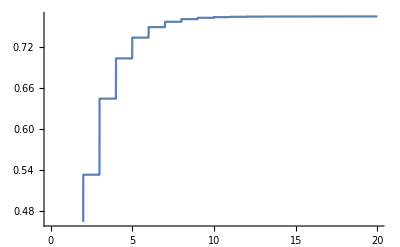

```mathematica
Plot[Sum[1/(2^k+1),{k,1,n}],{n,0,20}]
```

```mathematica
f[n+1]-f[n]//Factor
```

-2^n/((1+2^n) (1+2^(1+n)))

```mathematica
RSolve[{g[n+1]-g[n]== f[n+1],g[0]== 1},g[n],n]
```

{{g[n]→(Log[2]+n Log[2]-QPolyGamma[0,n-(ⅈ π-Log[2])/Log[2],2]+QPolyGamma[0,-(ⅈ π-Log[2])/Log[2],2])/Log[2]}}

## Th.1 (Haga's 1st theorem) example from testprogram.nb

```mathematica
EosSession["Haga1"];
```

```mathematica
NewOrigami[]
```

Haga1.1

-Graphics3D-

```mathematica
HO["C","D",MarkPointOn->"CD"]
```

Haga1.2

-Graphics3D-

```mathematica
Unfold[]
```

Haga1.3

-Graphics3D-

```mathematica
HO["B","E",MarkPointOn->"AD"]
```

Haga1.4

-Graphics3D-

```mathematica
HO["AB", Handle-> "D",MarkPointOn->"DF"]
```

Haga1.5

-Graphics3D-

```mathematica
UnfoldAll[]
```

Haga1.7

{-Graphics3D-,-Graphics3D-}

#### Proof

```mathematica
ProofDocFormat["Proof","Subsection",1]
```

Haga1.7

ProofDocFormat[Proof,Subsection,1]

```mathematica
ProofDocFormat["Goal","Subsubsection",1];
```

```mathematica
Goal[(3Distance["G","A"])^2==Distance["A","D"]^2];
```

```mathematica
Prove["Segment trisection Th.1"]
```

ProofbyGB::gbstart: Proof by Groebner basis method started at "June 6, 2018 3:35:03 PM JST".

ProofbyGB::gbsuccess: Proof by Groebner basis method is successful.

CPU time used for Groebner basis computation is 0.06823  seconds.

Haga1.7

{True,0.06823,}

```mathematica
EndSession[]
```

7